```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=1
(*Integration Bounds*)
l:=3
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
```

```mathematica
(*Instanton potential--no molecule*)
 Asing[y_]:=Table[Sum[2ηbar[[μ,ν,aa]]*y[[ν]]/((y.y+1)(y.y)),{ν,1,4}],{μ,1,4},{aa,1,3}]
```

```mathematica
(*Instanton rotation*)
Rvec:=
R{0,0,0,1}
```

```mathematica
(*Ratio Ansatz--Molecule*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arot[y_]:=
Table[
Sum[(-η[[mu]][[nu]][[a]]*2*Ya[y][[nu]]/(Ya[y].Ya[y])^2-
ηbar[[mu]][[nu]][[a]]*2*Yi[y][[nu]]/(Yi[y].Yi[y])^2),{nu,1,4}]/(1+1/(Ya[y].Ya[y])+1/(Yi[y].Yi[y]))
,{mu,1,4},{a,1,3}](*Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]*)
Dimensions[Arot[ypoint]]
```

{4,3}

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,rot_,t_]:=Dot@@Table[W2[Asing[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WApproxLower[y_,rot_,t_]:=Dot@@Table[W2[Asing[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
WdApproxUpper[y_,rot_,t_]:=Dot@@Table[Wd2[Asing[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WdApproxLower[y_,rot_,t_]:=Dot@@Table[Wd2[Asing[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
```

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpperM[y_,rot_,t_]:=Dot@@Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WApproxLowerM[y_,rot_,t_]:=Dot@@Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
WdApproxUpperM[y_,rot_,t_]:=Dot@@Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WdApproxLowerM[y_,rot_,t_]:=Dot@@Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
```

```mathematica
(*Obtaining random spherically distributed points.*)
RandSphere:=Module[{r,poi},r=2;
While[r>1,
poi=RandomReal[{-1,1},4];
r=Norm[poi]]; 
poi=poi/r;
poi ]
{RandSphere,RandSphere}
(*ListPlot[Table[randSphere,100],AspectRatio->1]*)
```

{{-0.356696,0.455625,0.671371,0.46307},{0.246065,-0.190856,0.549751,0.775113}}

```mathematica
(*Random sampling of rotation matricies*)
RotR[a_]:=
{{a[[1]],-a[[2]],-a[[3]],-a[[4]]},
{a[[2]],a[[1]],-a[[4]],a[[3]]},
{a[[3]],a[[4]],a[[1]],-a[[2]]},
{a[[4]],-a[[3]],a[[2]],a[[1]]}};
RotL[p_]:={{p[[1]],-p[[2]],-p[[4]],-p[[3]]},
{p[[2]],p[[1]],p[[3]],-p[[4]]},
{p[[4]],-p[[3]],p[[1]],p[[2]]},
{p[[3]],p[[4]],-p[[2]],p[[1]]}};
Rot[a_,p_]:=RotL[a].RotR[p]
RandRot:=Rot[RandSphere,RandSphere]
```

```mathematica
RandY:=Append[RandomReal[{-l,l},3],0]
```

```mathematica
(*Unit conversion to GeV and multiplication by instanton density 12/2*)
units=43.7;
(*Conversion from ρ to GeV^-1*)
unitsr=1.4;
(*Step size in r*)
rstep=0.8;
```

```mathematica
(*Field Strength instanton*)
Fmunu=(Table[D[Asing[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Asing[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Asing[{y[1],y[2],y[3],y[4]}][[mu]][[b]]Asing[{y[1],y[2],y[3],y[4]}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}]);
Dimensions[Fmunu]
```

{4,4,3}

```mathematica
(*Field Strength mol *)
FmunuM=(Table[D[Arot[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arot[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arot[{y[1],y[2],y[3],y[4]}][[mu]][[b]]Arot[{y[1],y[2],y[3],y[4]}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}]);
Dimensions[FmunuM]
Dimensions[Arot[{y[1],y[2],y[3],y[4]}]]
```

{4,4,3}

{4,3}

```mathematica
B[yy_,rot_]:=Table[1/2Sum[rot[[i1,i2]]Transpose[rot][[j1,j2]]LeviCivitaTensor[3][[i2]][[j2]][[k]](Fmunu[[i1,j1,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]})PauliMatrix[a] ,{j1,1,3},{j2,1,3},{i1,1,3},{i2,1,3},{a,1,3}],{k,1,3}]
Ee[yy_,rot_]:=Table[1/2Sum[(Sum[rot[[i1,i]]rot[[j1,4]]Fmunu[[i1,j1,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]},{j1,1,3},{i1,1,3}])PauliMatrix[a] ,{a,1,3}],{i,1,3}]
```

```mathematica
BM[yy_,rot_]:=Table[1/2Sum[rot[[i1,i2]]rot[[j1,j2]]LeviCivitaTensor[3][[i2]][[j2]][[k]](FmunuM[[i1,j1,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]})PauliMatrix[a] ,{j1,1,3},{j2,1,3},{i1,1,3},{i2,1,3},{a,1,3}],{k,1,3}]
EeM[yy_,rot_]:=Table[1/2Sum[(Sum[rot[[i1,i]]rot[[j1,4]]FmunuM[[i1,j1,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]},{j1,1,3},{i1,1,3}])PauliMatrix[a] ,{a,1,3}],{i,1,3}]
```

```mathematica
BM[RandY,RandRot][[1]]
Ee[RandY,RandRot][[1]]
```

{{-0.055892,-0.0183654+0.0480849 ⅈ},{-0.0183654-0.0480849 ⅈ,0.055892}}

{{0.00142409,-0.00249026-0.000719063 ⅈ},{-0.00249026+0.000719063 ⅈ,-0.00142409}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y_,rot_,rr_]:=(L/n)^2Sum[Tr[Sum[WApproxLower[y+rot.{rr/2,0,0,0},rot,t1].B[y+rot.{rr/2,0,0,0}+rot.{0,0,0,t1},rot][[i]].WApproxUpper[y+rot.{rr/2,0,0,0},rot,t1],{t1,L/n,L,L/n}].Sum[WdApproxUpper[y-rot.{rr/2,0,0,0},rot,t2].B[y-rot.{rr/2,0,0,0}+rot.{0,0,0,t2},rot][[i]].WdApproxLower[y-rot.{rr/2,0,0,0},rot,t2],{t2,L/n,L,L/n}]],{i,1,3}]
```

```mathematica
ImesBBM[y_,rot_,rr_]:=(L/n)^2Sum[Tr[Sum[WApproxLowerM[y+rot.{rr/2,0,0,0},rot,t1].BM[y+rot.{rr/2,0,0,0}+rot.{0,0,0,t1},rot][[i]].WApproxUpperM[y+rot.{rr/2,0,0,0},rot,t1],{t1,L/n,L,L/n}].Sum[WdApproxUpperM[y-rot.{rr/2,0,0,0},rot,t2].BM[y-rot.{rr/2,0,0,0}+rot.{0,0,0,t2},rot][[i]].WdApproxLowerM[y-rot.{rr/2,0,0,0},rot,t2],{t2,L/n,L,L/n}]],{i,1,3}]
```

```mathematica
AbsoluteTiming[ImesBB[RandY,RandRot,3]]
AbsoluteTiming[ImesBBM[RandY,RandRot,3]]
```

{2.08405,0.000964094+0. ⅈ}

{4.47601,0.00120618+0. ⅈ}

```mathematica
(*Number of test points for monte carlo*)
num=200;
(* box size *)
l=1;
(*Random numbers for all future points*)
randRot=Table[RandRot,11,num];
randY=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];
randRot2=Table[RandRot,11,num];
randY2=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];
```

```mathematica
(*Rotation Angle Magnitude*)
SU3Angle[y_,rot_,rr_,t_]:=ArcSin[Sqrt[1-1/4Tr[WApproxUpperM[y+rot.{rr/2,0,0,0},rot,t]]^2]]
AngleTable=Table[SU3Angle[randY[[3,i]],randRot[[3,i]],1.6,t],{t,0,3L/4,L/4},{i,1,num}];
```

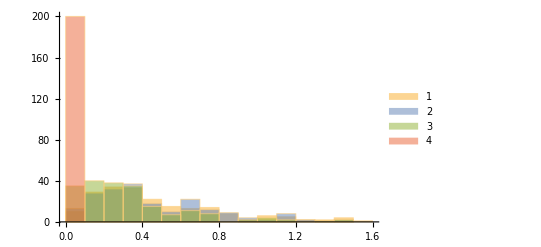

```mathematica
Histogram[Re[AngleTable],PlotRange->All,ChartLegends->Automatic]
```

```mathematica
RandY
```

{0.735853,0.50264,0.0320251,0}

```mathematica
DistanceBB=ParallelTable[Module[{rot, y},rot=RandRot;
y=rot.RandY; (* it was strange factor 2 I deleted in the next line 
also no units to compare to my calculations, and why divide by num?
{units*8*l^3/num*ImesBB[y,rot,rr/unitsr],units*8*l^3/num*ImesBBM[y,rot,rr/unitsr]} *)
 {rr,Re[ImesBB[y,rot,rr]],Re[ImesBBM[y,rot,rr]]}
],{rr,0.1,8,0.2},{i,1,num}]
```

```mathematica
DistanceBB[[1,1,3]]
```

77.4873

```mathematica
nzmax=20;
BBmean=Table[Evaluate[Sum[DistanceBB[[kk,ii,2]],{ii,1,num}]/num],{kk,1,nzmax}];
BBerr=Table[Sqrt[Sum[(DistanceBB[[kk,ii,2]]-BBmean[[kk]])^2,{ii,1,num}]]/num,{kk,1,nzmax}];
BBresult=Table[{DistanceBB[[kk,1,1]],Around[BBmean[[kk]],BBerr[[kk]]]},{kk,1,nzmax}]

BBMmean=Table[Evaluate[Sum[DistanceBB[[kk,ii,3]],{ii,1,num}]/num],{kk,1,nzmax}];
BBMerr=Table[Sqrt[Sum[(DistanceBB[[kk,ii,3]]-BBMmean[[kk]])^2,{ii,1,num}]]/num,{kk,1,nzmax}];
BBMresult=Table[{DistanceBB[[kk,1,1]],Around[BBMmean[[kk]],BBMerr[[kk]]]},{kk,1,nzmax}]
```

Part::pkspec1: The expression kk cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
BBresult={{0.1,0.390.04},{0.30000000000000004,0.3550.030},{0.5,0.3540.024},{0.7,0.3010.020},{0.9,0.2270.020},{1.1,0.1600.017},{1.3000000000000003,0.1320.014},{1.5000000000000002,0.0720.013},{1.7000000000000002,0.0570.010},{1.9000000000000001,0.0160.008},{2.1,0.0040.007},{2.3000000000000003,-0.0100.005},{2.5000000000000004,-0.0030.004},{2.7000000000000006,-0.01500.0031},{2.9000000000000004,-0.02020.0027},{3.1000000000000005,-0.01570.0022},{3.3000000000000003,-0.01700.0020},{3.5000000000000004,-0.01290.0015},{3.7,-0.01160.0014},{3.9000000000000004,-0.00990.0011}};
```

```mathematica
BBMresult={{0.1,14.02.3},{0.30000000000000004,5.71.2},{0.5,7.01.4},{0.7,3.70.4},{0.9,2.790.27},{1.1,2.000.28},{1.3000000000000003,1.230.17},{1.5000000000000002,0.530.19},{1.7000000000000002,0.400.12},{1.9000000000000001,0.300.09},{2.1,0.240.07},{2.3000000000000003,0.120.06},{2.5000000000000004,0.050.04},{2.7000000000000006,0.000.04},{2.9000000000000004,-0.0590.028},{3.1000000000000005,-0.0850.020},{3.3000000000000003,-0.0340.018},{3.5000000000000004,-0.0580.015},{3.7,-0.0600.011},{3.9000000000000004,-0.0460.009}};
```

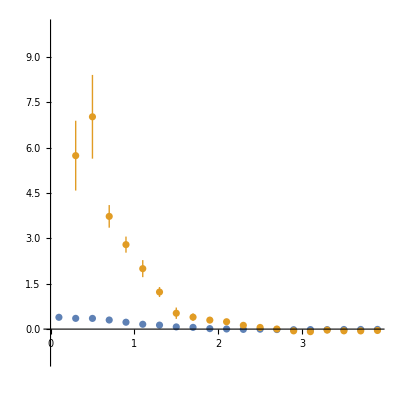

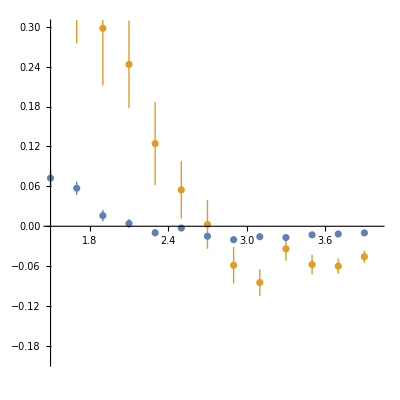

```mathematica
ListPlot[{BBresult,BBMresult},PlotRange->{-1,10},AspectRatio->1]
ListPlot[{BBresult,BBMresult},PlotRange->{{1.5,4},{-0.2,0.3}},AspectRatio->1]
(*dataBB=Table[{DistanceBB[[rr/0.8+1,i,1]],Around[Sum[DistanceBB[[rr/0.8+1,i,2]]/num,{i,1,num}],Table[*Variance[Transpose[DistanceDataMesBB,2<->3][[rr/0.8+1,1]]]]},{rr,0,8,0.8}]]
dataBBM=Re[Table[{rr,Around[Sum[DistanceDataMesBB[[rr/0.8+1,i,2]],{i,1,num}],Sqrt[num]*Variance[Transpose[DistanceDataMesBB,2<->3][[rr/0.8+1,2]]]]},{rr,0,8,0.8}]] *)
```

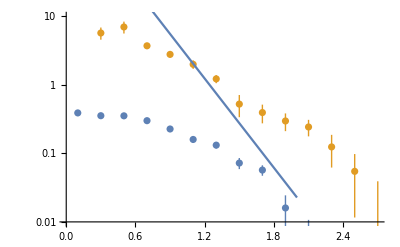

```mathematica
Show[ListLogPlot[{BBresult,BBMresult},PlotRange->{.01,10}],LogPlot[500*Exp[-3*(5/3)*x],{x,0,2}]]
```

```mathematica
(* let me replot it multiplied by r^2 *)
BBr2=Table[{BBresult[[kk,1]],BBresult[[kk,2]]*BBresult[[kk,1]]^2},{kk,1,20}]
BBMr2=Table[{BBMresult[[kk,1]],BBMresult[[kk,2]]*BBMresult[[kk,1]]^2},{kk,1,20}]


(* so molecular is much larger ??? 
this is in contradiction to what I got without Ws
let me do without W here, indicated by 0 in the name
*)
```

{{0.1,0.00390.0004},{0.3,0.03200.0027},{0.5,0.0880.006},{0.7,0.1470.010},{0.9,0.1840.016},{1.1,0.1930.020},{1.3,0.2230.023},{1.5,0.1630.030},{1.7,0.1650.029},{1.9,0.0580.030},{2.1,0.0180.029},{2.3,-0.0510.028},{2.5,-0.0170.027},{2.7,-0.1090.022},{2.9,-0.1700.023},{3.1,-0.1510.021},{3.3,-0.1850.022},{3.5,-0.1580.019},{3.7,-0.1590.019},{3.9,-0.1510.016}}

{{0.1,0.1400.023},{0.3,0.520.10},{0.5,1.750.35},{0.7,1.830.18},{0.9,2.260.22},{1.1,2.420.34},{1.3,2.070.28},{1.5,1.20.4},{1.7,1.140.35},{1.9,1.070.31},{2.1,1.070.29},{2.3,0.660.33},{2.5,0.340.27},{2.7,0.020.27},{2.9,-0.490.23},{3.1,-0.810.19},{3.3,-0.370.19},{3.5,-0.700.18},{3.7,-0.820.16},{3.9,-0.700.14}}

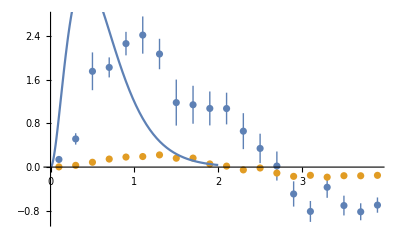

```mathematica
Show[ListPlot[{BBMr2,BBr2}],Plot[150*Exp[-2.9*(5/3)*x]*x^2,{x,0,2}]]
```

```mathematica
(* run higher statistics on the left side, longer W perhaps 
on the plot show wfs of upsilon and j/psi
*)
```

```mathematica
ImesBB0[y_,rot_,rr_]:=(L/n)^2Sum[Tr[Sum[B[y+rot.{rr/2,0,0,0}+rot.{0,0,0,t1},rot][[i]] ,{t1,L/n,L,L/n}].Sum[B[y-rot.{rr/2,0,0,0}+rot.{0,0,0,t2},rot][[i]],
{t2,L/n,L,L/n}]],{i,1,3}]
ImesBBM0[y_,rot_,rr_]:=(L/n)^2Sum[Tr[Sum[BM[y+rot.{rr/2,0,0,0}+rot.{0,0,0,t1},rot][[i]],{t1,L/n,L,L/n}].Sum[BM[y-rot.{rr/2,0,0,0}+rot.{0,0,0,t2},rot][[i]],{t2,L/n,L,L/n}]],{i,1,3}]
BB0=ParallelTable[Module[{rot, y},rot=RandRot;
y=rot.RandY; (* it was strange factor 2 I deleted in the next line 
also no units to compare to my calculations, and why divide by num?
{units*8*l^3/num*ImesBB[y,rot,rr/unitsr],units*8*l^3/num*ImesBBM[y,rot,rr/unitsr]} *)
 {rr,Re[ImesBB0[y,rot,rr]],Re[ImesBBM0[y,rot,rr]]}
],{rr,0.1,4,0.2},{i,1,num}]
```

Part::pkspec1: The expression kk cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{0.1,0.6770.035},{0.3,0.690.04},{0.5,0.610.04},{0.7,0.5040.025},{0.9,0.3670.018},{1.1,0.2490.015},{1.3,0.1610.010},{1.5,0.0970.009},{1.7,0.0350.007},{1.9,0.0060.007},{2.1,-0.0260.006},{2.3,-0.0240.006},{2.5,-0.0390.004},{2.7,-0.0300.004},{2.9,-0.0280.004},{3.1,-0.02220.0028},{3.3,-0.02410.0021},{3.5,-0.01940.0022},{3.7,-0.01750.0015},{3.9,-0.01120.0013}}

Part::pkspec1: The expression kk cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{0.1,10.81.1},{0.3,11.71.3},{0.5,11.71.4},{0.7,6.90.5},{0.9,6.70.8},{1.1,3.80.4},{1.3,2.410.17},{1.5,1.700.14},{1.7,1.060.10},{1.9,0.430.07},{2.1,0.310.06},{2.3,0.220.06},{2.5,-0.020.04},{2.7,0.050.04},{2.9,-0.0280.031},{3.1,0.0050.027},{3.3,-0.0600.020},{3.5,-0.0460.018},{3.7,-0.0510.012},{3.9,-0.0170.011}}

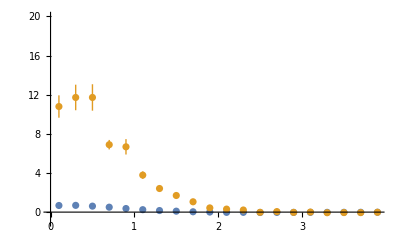

```mathematica
BB0mean=Table[Evaluate[Sum[BB0[[kk,ii,2]],{ii,1,num}]/num],{kk,1,nzmax}];
BB0err=Table[Sqrt[Sum[(BB0[[kk,ii,2]]-BB0mean[[kk]])^2,{ii,1,num}]]/num,{kk,1,nzmax}];
BB0result=Table[{BB0[[kk,1,1]],Around[BB0mean[[kk]],BB0err[[kk]]]},{kk,1,nzmax}]

BBM0mean=Table[Evaluate[Sum[BB0[[kk,ii,3]],{ii,1,num}]/num],{kk,1,nzmax}];
BBM0err=Table[Sqrt[Sum[(BB0[[kk,ii,3]]-BBM0mean[[kk]])^2,{ii,1,num}]]/num,{kk,1,nzmax}];
BBM0result=Table[{BB0[[kk,1,1]],Around[BBM0mean[[kk]],BBM0err[[kk]]]},{kk,1,nzmax}]

ListPlot[{BB0result,BBM0result},PlotRange->{-1,20}]
```

```mathematica
(* old results small statistics *)
```

```mathematica
Nicholas:={{0.,0.01.310^4},{0.8,0.22.110^3},{1.6,362.849.},{2.4000000000000004,312.340.},{3.2,88.97.},{4.,6.81.},{4.800000000000001,16.17.},{5.6000000000000005,12.14.},{6.4,-20.6.},{7.2,-14.12.4},{8.,-17.41.5}}
```

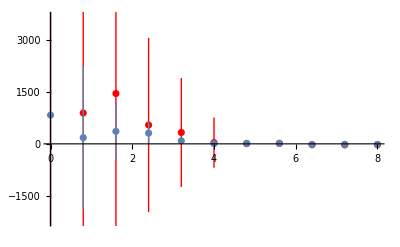

-Graphics-

-Graphics-

```mathematica
Show[ ListPlot[dataBBM,PlotStyle->Red],ListPlot[dataBB]]
```